```mathematica
cs0 = x/.First@FindRoot[LegendreP[1/2,x]==0,{x,-0.5},WorkingPrecision->50];
dd=2.7142175397111330*(-0.5) * LegendreP[1/2,(-cs0)]/(1-(Abs@cs0)^2)^(1/4);
```

```mathematica
SetDirectory[NotebookDirectory[]];
res=Import["answer0.txt","Table"];
LinearModelFit[Log10@Abs@res⟦-10;;-1⟧,x,{x}]
plotData=Table[{res⟦i,1⟧,Abs@res⟦i,2⟧-0Abs@dd*res⟦i,1⟧^(1/2)},{i,1,Length@res}];
Show[ListPlot[Log10@Abs@plotData,AspectRatio->Automatic,GridLines->Automatic,Joined->True,PlotRange->All
],
Plot[-2.5x+0.5,{x,-5,5},PlotStyle->Red]]
```

FittedModel[-0.0524788+0.992277 x]

-Graphics-

```mathematica
res
```

{{1.71918×10^-18,-1.55846},{0.302694,-1.56573},{0.611877,-1.58889},{0.931931,-1.63202},{1.26345,-1.70219},{1.60231,-1.80806},{1.93831,-1.96208},{2.24823,-2.18463},{2.5236,-2.46016},{2.81487,-2.72373},{3.12881,-2.96845},{3.43899,-3.22473},{3.7508,-3.48273},{4.06289,-3.74222},{4.37549,-4.00216},{4.68769,-4.26344},{5.0003,-4.52498},{5.3126,-4.78751},{5.62519,-5.05023},{5.93755,-5.31372},{6.25013,-5.57735},{6.56252,-5.84158},{6.8751,-6.10592},{7.18751,-6.37075},{7.50008,-6.63564},{7.8125,-6.90095},{8.12506,-7.1663},{8.43749,-7.432},{8.75005,-7.69772},{9.06249,-7.96375},{9.37504,-8.22979},{9.68748,-8.4961},{10,-8.7624},{10.3125,-9.02894},{10.625,-9.29546},{10.9375,-9.5622},{11.25,-9.82892},{11.5625,-10.0958},{11.875,-10.3627},{12.1875,-10.6298},{12.5,-10.8968},{12.8125,-11.164},{13.125,-11.4312},{13.4375,-11.6985},{13.75,-11.9658},{14.0625,-12.2332},{14.375,-12.5006},{14.6875,-12.7681},{15,-13.0356},{15.3125,-13.3032},{15.625,-13.5708},{15.9375,-13.8385},{16.25,-14.1061},{16.5625,-14.3739},{16.875,-14.6416},{17.1875,-14.9094},{17.5,-15.1771},{17.8125,-15.445},{18.125,-15.7128},{18.4375,-15.9808},{18.75,-16.2486},{19.0625,-16.5166},{19.375,-16.7845},{19.6875,-17.0526},{20,-17.3205},{20.3125,-17.5886},{20.625,-17.8566},{20.9375,-18.1247},{21.25,-18.3927},{21.5625,-18.6609},{21.875,-18.9289},{22.1875,-19.1971},{22.5,-19.4652},{22.8125,-19.7334},{23.125,-20.0016},{23.4375,-20.2698},{23.75,-20.538},{24.0625,-20.8062},{24.375,-21.0744},{24.6875,-21.3427}}

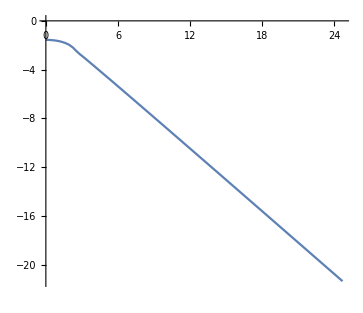

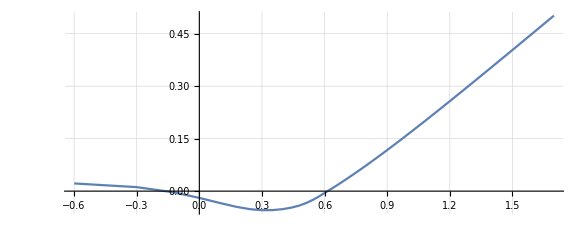

```mathematica
ListPlot[res,Joined->True,PlotRange->All,AspectRatio->Automatic]
```

```mathematica
ArcCos@cs0
```

2.2813183068406470463924167927275591485937279252011

```mathematica
ff=c0 r+c1 /√r;
Series[D[ff,{r,2}]/((√(1+D[ff,{r,1}]^2))^3)+1/r D[ff,r]/(√(1+D[ff,{r,1}]^2)),{r,∞,5}]
```

c0/(√(1+c0^2) r)+(c1 (1/r)^(5/2))/(4 (1+c0^2)^(3/2))+(3 c0 c1^2)/(4 (1+c0^2)^(5/2) r^4)+O[1/r]^(11/2)